# Erzeugung von "farbigem Rauschen" (normalverteilt)

```mathematica
PlotSample[sample_List]:=
ListLinePlot[
sample,
PlotLabel->"μ = "<>
	ToString[Chop[Mean[sample]]]
<>", σ = "<>
ToString[
StandardDeviation[sample]
],
AxesLabel->{TraditionalForm["n"],"X_n"}
];
```

### Gleichverteiltes weißes Rauschen

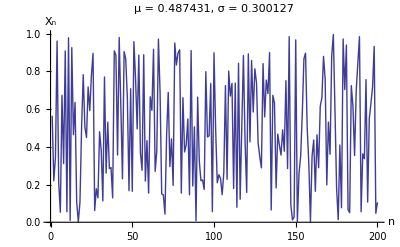

```mathematica
uniform=RandomReal[1,200];
PlotSample[uniform]
```

### Normalverteiltes weißes Rauschen

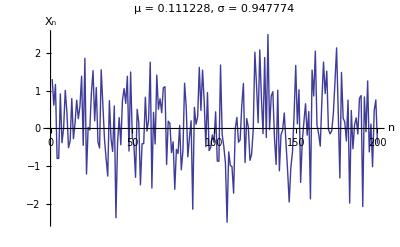

```mathematica
normal=RandomReal[
NormalDistribution[0,1],
200];
PlotSample[normal]
```

### Umwandlung in 1/f- Rauschen

```mathematica
ftnorm=Fourier[normal];
pinkmanip=Table[If[200-i==0,1,Sqrt[(200-i)]^-1],{i,200}]*ftnorm;
pink=InverseFourier[pinkmanip];
```

```mathematica
ftnorm=FourierDCT[
RandomReal[
NormalDistribution[0,1],
200]
,2];
```

```mathematica
pinkmanip=Table[Sqrt[i]^-1,{i,200}]*ftnorm;
```

```mathematica
pink=FourierDCT[pinkmanip,3];
```

```mathematica
p2=2*Pi*(pink-Mean[pink]);
```

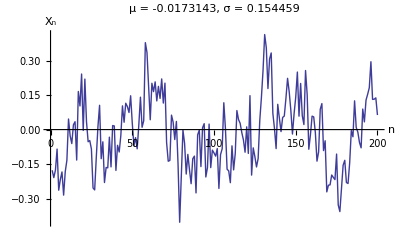

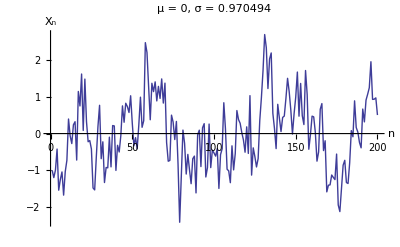

```mathematica
PlotSample[pink]
PlotSample[p2]
```

### Korreliertes, eindimensionales Rauschen

```mathematica
Gauss1D[gamma_,N_]:=Block[{ft,manip},
ft=FourierDCT[
RandomReal[NormalDistribution[0,1],
N],2
];
manip=
Table[If[i==1,1/√N,
Sqrt[
gamma[
Abs[
i-1
]
]
]*ft[[i]]],{i,N}
];
manip=FourierDCT[manip,3]*Sqrt[N]/(2 √2);
ps=PlotSample[manip];
manip
];
```

```mathematica
GRF1D[alpha_,N_]:=Block[{ft,manip},
ft=Fourier[
RandomReal[NormalDistribution[0,1],N]
];
manip=
Table[
If[i==1,1/√N,1/i^(alpha/2)]*ft[[i]],{i,N}
];
manip=Re[InverseFourier[manip]](**Sqrt[N]/(2 √2)*);
ps=PlotSample[manip];
manip
];
```

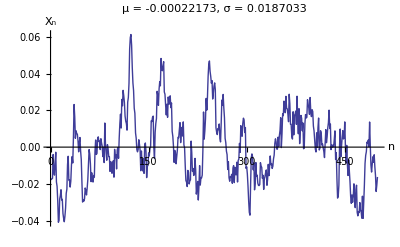

```mathematica
GRF1D[2,500];
Show[ps]
```

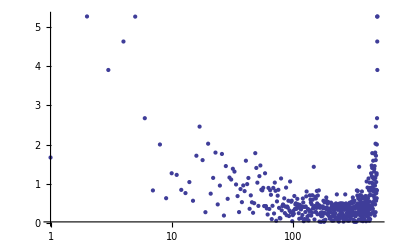

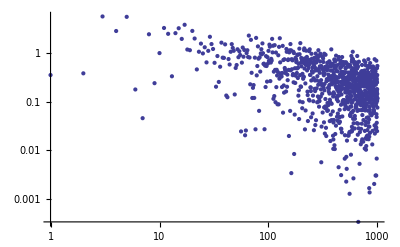

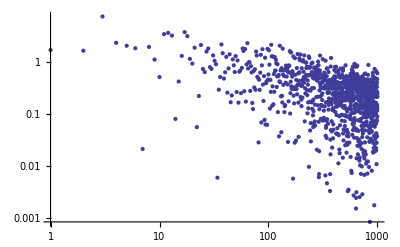

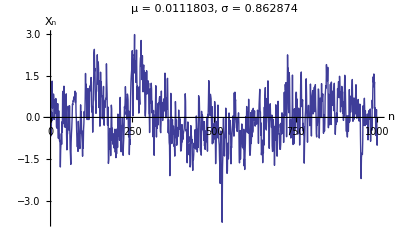

```mathematica
noise=Gauss1D[1/# &,1000];
ListLogLinearPlot[Abs[Fourier[Take[noise,Length[noise]/2]]],PlotRange->All]
ListLogLogPlot[Abs[FourierDCT[noise]],PlotRange->All]
ListLogLogPlot[Abs[FourierDST[noise]],PlotRange->All]
Show[ps]
```

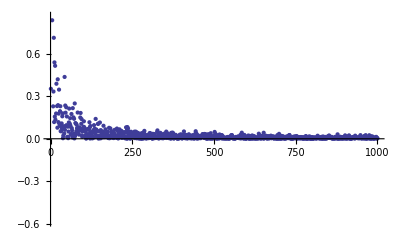

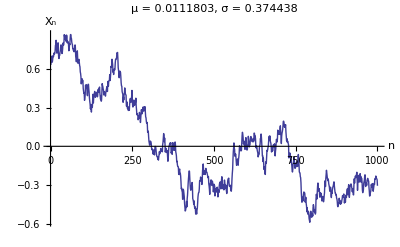

```mathematica
red=Gauss1D[1/#^2 &,1000];
ListPlot[
Abs[FourierDCT[red]],PlotRange->{Min[red],Max[red]}
]
Show[ps]
```

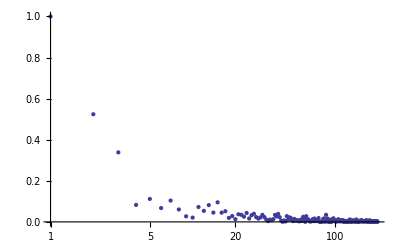

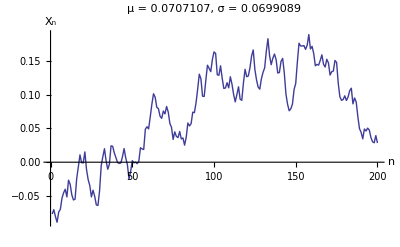

```mathematica
ListLogLinearPlot[Abs[FourierDCT[Gauss1D[1/#^2 &,200]]],PlotRange->All]
Show[ps]
```

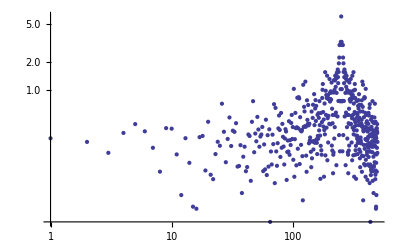

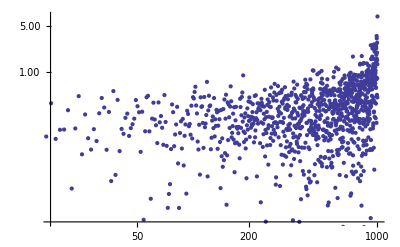

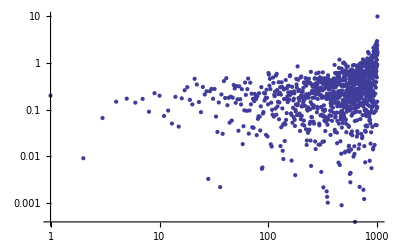

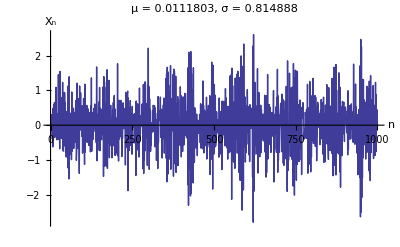

```mathematica
noise=Gauss1D[1/(1001-#) &,1000];
ListLogLogPlot[Abs[Fourier[Take[noise,Length[noise]/2]]],PlotRange->All]
ListLogLogPlot[Abs[FourierDCT[noise]]]
ListLogLogPlot[Abs[FourierDST[noise]],PlotRange->All]
Show[ps]
```

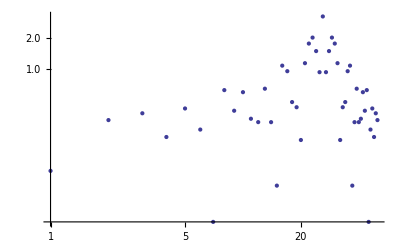

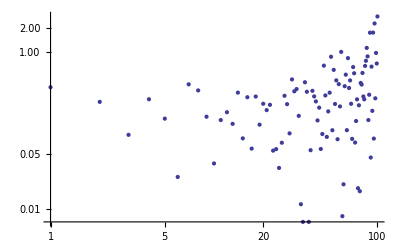

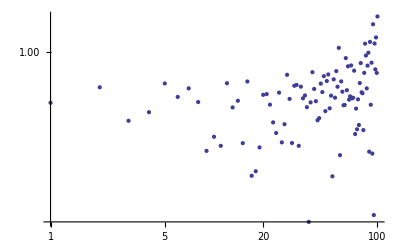

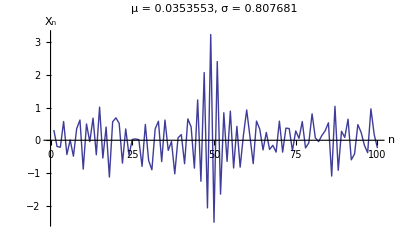

```mathematica
noise=Gauss1D[1/(101-#) &,100];
ListLogLogPlot[Abs[Fourier[Take[noise,Length[noise]/2]]],PlotRange->All]
ListLogLogPlot[Abs[FourierDCT[noise]]]
ListLogLogPlot[Abs[FourierDST[noise]],PlotRange->All]
Show[ps]
```

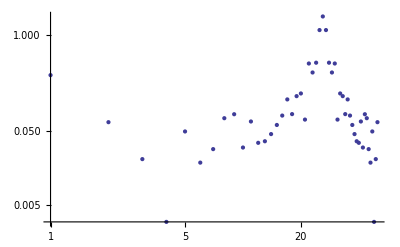

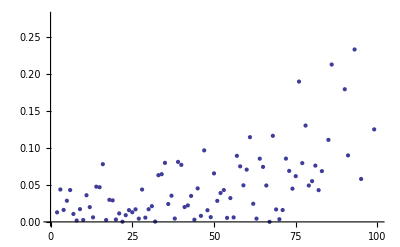

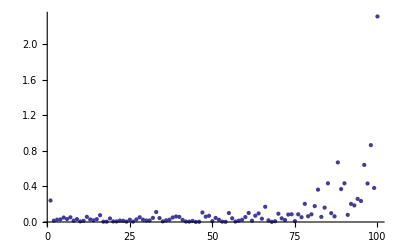

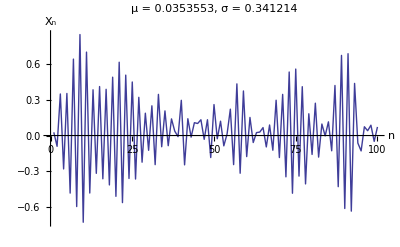

```mathematica
noise=Gauss1D[1/(101-#)^2 &,100];
ListLogLogPlot[Abs[Fourier[Take[noise,Length[noise]/2]]],PlotRange->All]
ListPlot[Abs[FourierDCT[noise]]]
ListPlot[Abs[FourierDST[noise]],PlotRange->All]
Show[ps]
```

## Zweidimensionale Felder

```mathematica
norm2D=RandomReal[NormalDistribution[0,1],{200,200}];
```

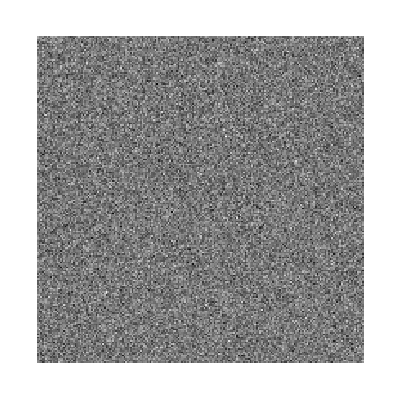

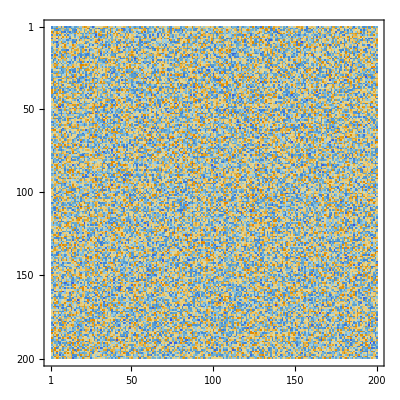

```mathematica
ArrayPlot[norm2D,PlotRange->{Min[norm2D],Max[norm2D]}]
MatrixPlot[norm2D,PlotRange->{Min[norm2D],Max[norm2D]}]
```

```mathematica
ftnorm2D=FourierDCT[norm2D];
```

```mathematica
pinkft=Table[
2*Pi*Pi*ftnorm2D[[i,j]]*Sqrt[Sqrt[i^2+j^2]]^-1,
{i,Length[ftnorm2D]},{j,Length[ftnorm2D[[1]]]}];
(*If[Sqrt[(200-i)^2+(200-j)^2]==0,Pi*ftnorm2D[[i,j]],ftnorm2D[[i,j]]*Pi*Sqrt[Sqrt[i^2+j^2]]^-1],
{i,Length[ftnorm2D]},{j,Length[ftnorm2D[[1]]]}];*)
pink2D=FourierDCT[pinkft,3];
```

{-7.60113,7.43723}

{0.0224826,1.82625}

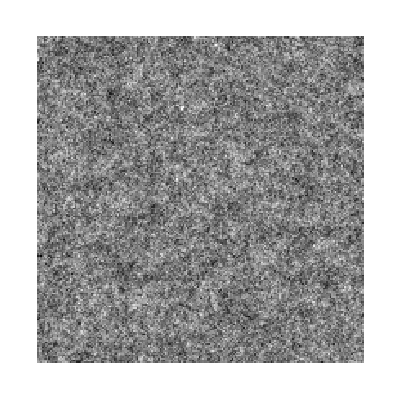

```mathematica
{Min[pink2D],Max[pink2D]}
{Mean[Flatten[pink2D]],StandardDeviation[Flatten[pink2D]]}
ArrayPlot[pink2D, PlotRange->{Min[pink2D],Max[pink2D]}]
```

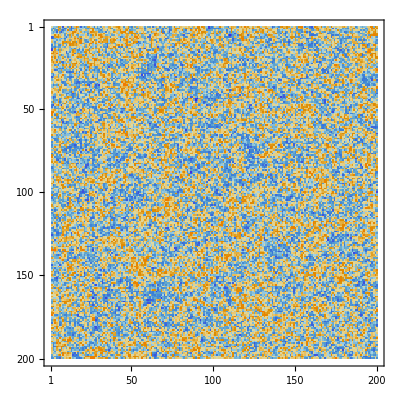

```mathematica
MatrixPlot[pink2D, PlotRange->{Min[pink2D],Max[pink2D]}]
```

### Gauß-Rauschen mit vorgegebener Korrelation

```mathematica
GaussNoise2D[fac_,gamma_,N_]:=Block[{n2D,ft,manip,n},
n=N/2;
n2D=RandomReal[NormalDistribution[0,1],{N,N}];
ft=Fourier[n2D];(*FourierDCT[n2D];*)
manip=Table[
fac*ft[[i,j]]*Sqrt[gamma[If[
Sqrt[(n-i)^2+(n-j)^2]==0,1,Sqrt[(n-i)^2+(n-j)^2]]]],
{i,N},{j,N}];
manip=InverseFourier[manip];(*FourierDCT[manip,3];*)
manip=(N/2)*Re[manip];
ap=ArrayPlot[manip,DisplayFunction->Identity,PlotRange->{Min[manip],Max[manip]}];
mp=MatrixPlot[manip,DisplayFunction->Identity,PlotRange->{Min[manip],Max[manip]}];
manip
];
```

```mathematica
GRF2D[alpha_,N_]:=Block[
{n2D,ft,manip,n,x},
n=1;
n2D=RandomReal[NormalDistribution[0,1],{N,N}];
ft=Fourier[n2D];(*FourierDCT[n2D];*)
x=Sqrt[i^2+j^2];
manip=
Table[
ft[[i,j]]*
If[x==0,1,x^(-alpha/2)],
{i,N},{j,N}
];
manip=InverseFourier[manip];(*FourierDCT[manip,3];*)
manip=Re[manip];
wp=MatrixPlot[n2D,DisplayFunction->Identity,PlotRange->{Min[n2D],Max[n2D]}];
ap=ArrayPlot[manip,DisplayFunction->Identity,PlotRange->{Min[manip],Max[manip]}];
mp=MatrixPlot[manip,DisplayFunction->Identity,PlotRange->{Min[manip],Max[manip]}];
manip
];
```

#### Rosa Rauschen

{-0.0396454,0.0936539,-0.0684101,-0.0634255,-0.137421,«39991»,-0.0371077,-0.0361646,-0.00360694,-0.104804}

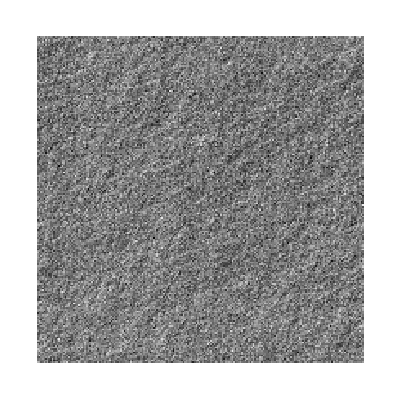

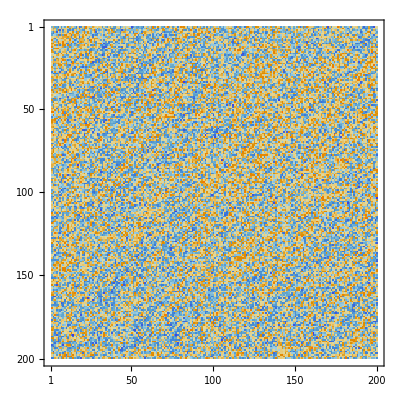

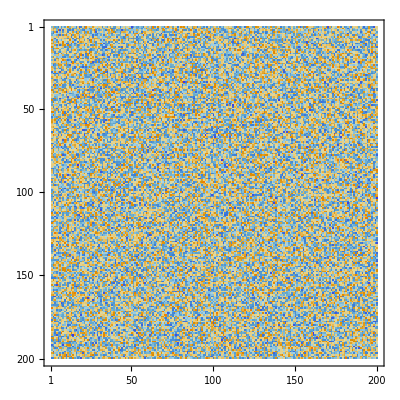

```mathematica
Flatten[GRF2D[1,200]]
Show[ap]
Show[mp]
Show[wp]
```

#### Rotes Rauschen

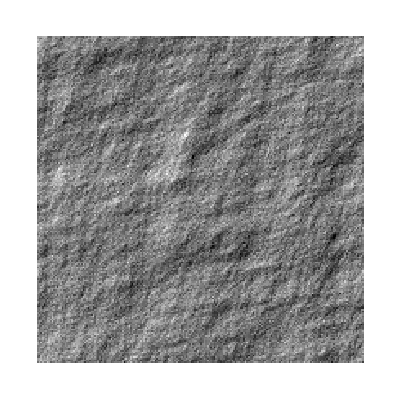

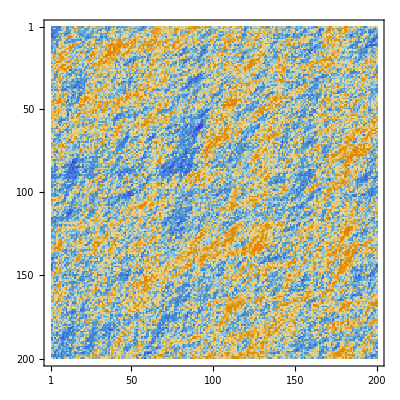

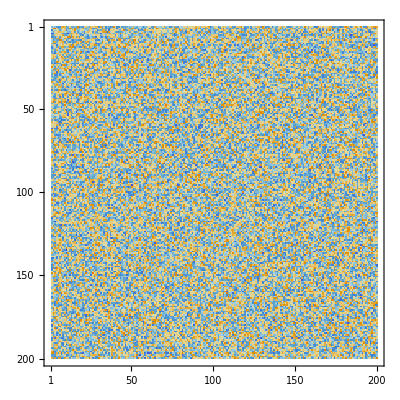

```mathematica
GRF2D[2,200];
Show[ap]
Show[mp]
Show[wp]
```

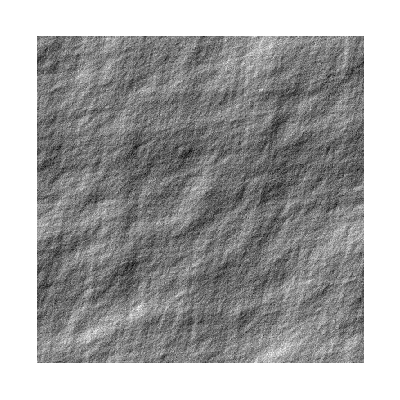

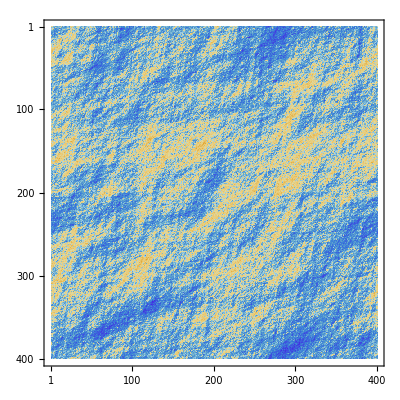

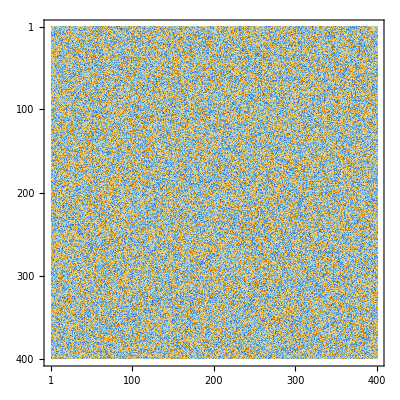

```mathematica
GRF2D[2,400];
Show[ap]
Show[mp]
Show[wp]
```

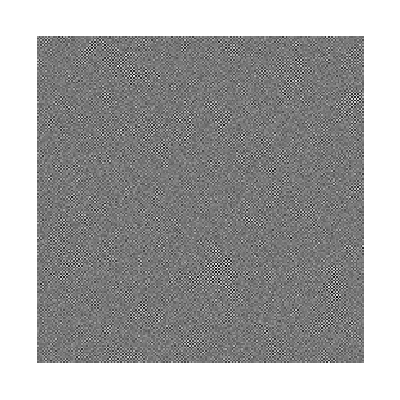

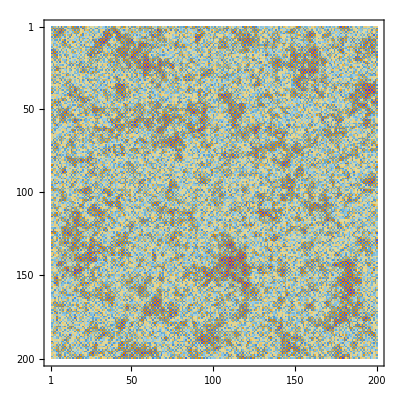

```mathematica
GaussNoise2D[1,(1/#^2)&,200];
Show[ap]
Show[mp]
```

```mathematica
GRF2D[-1,200];
Show[ap]
Show[mp]
```

-Graphics-

-Graphics-

```mathematica
GRF2D[-2,200];
Show[ap]
Show[mp]
```

-Graphics-

-Graphics-

```mathematica
GRF2D[4,200];
Show[ap]
Show[mp]
```

-Graphics-

-Graphics-

### Blaues Rauschen